## 1. Přednáška

### Tři důležité příkazy

```mathematica
Quiet[Remove["Global`*"]];
```

Vymaže předchozí definice

```mathematica
$HistoryLength = 2;
```

Omezuje paměť jádra, opatření proti přetečení paměti

```mathematica
SetDirectory[NotebookDirectory[]];
```

SetDir. ~ zavede místo nalezené NotebookDir. ~ cesta k lokaci. jako defaultní adresář

### Struktura výrazu, základy syntaxu

? ~ Help, fomát ? + symbol

```mathematica
?=
```

```mathematica
Vyraz = x+y + Sin[x^2+2*x*y+3]
```

x+y+Sin[3+x^2+2 x y]

```mathematica
Vyraz = x + y + Sin[x^2 + 2xy +3];
```

; ~ Input bez výstupu

```mathematica
?;
```

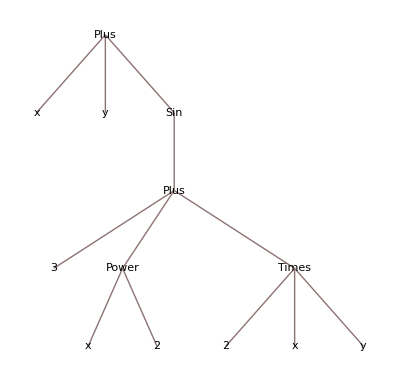

```mathematica
TreeForm[Vyraz]
```

```mathematica
?TreeForm
```

```mathematica
FullForm[Vyraz]
```

Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,x,y]]]]

```mathematica
Plus[x,y,Sin[Plus[3,Power[x,2],Times[2,xy]]]]
```

x+y+Sin[3+x^2+2 xy]

```mathematica
?FullForm
```

```mathematica
Head[Vyraz]
```

Plus

```mathematica
?Head
```

```mathematica
Attributes[Plus]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
?Attributes
```

### List

```mathematica
ListTree = {1, {2, 3}, {0,{ A, B}}}
```

{1,{2,3},{0,{A,B}}}

{1,{2,3},{0,{A,B}}}

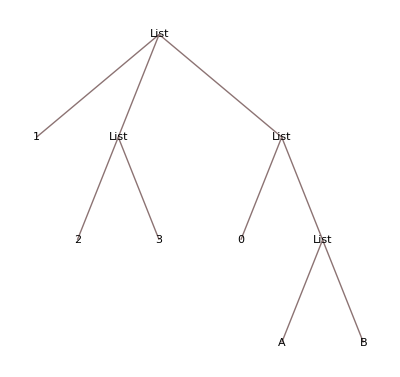

```mathematica
{1,{2,3},{0,{A,B}}}
TreeForm[ListTree]
```

```mathematica
ListTree[[1]]
ListTree[[2]]
ListTree[[3]]
ListTree[[-1]]
```

1

{2,3}

{0,{A,B}}

{0,{A,B}}

```mathematica
ListTree[[0]]
```

List

```mathematica
ListTree[[3, 2, 1]]
```

A

```mathematica
ListTree[[-1,-1,-1]]=C;
ListTree
```

{1,{2,3},{0,{A,C}}}

```mathematica
?Part
```

```mathematica
Length[ListTree]
```

3

```mathematica
?Length
```

```mathematica
Head[ListTree]
ListTree[[0]]
```

List

List

```mathematica
First[ListTree]
ListTree[[1]]
```

1

1

```mathematica
Last[ListTree]
ListTree[[-1]]
```

{0,{A,C}}

{0,{A,C}}